-Graphics-
-Graphics-

(Bienvenidos a eScience - Estadistica!
https://github.com/josemramirez/mmaescience/statistics -[for Statistical M.])_beta^v14

# Statistical Mechanics - Lec. 8 III.C The Bogoliubov-Born-Green-Kirkwood-Yvon Hierarchy

```mathematica
(1) -- Let's simplify the concept of phase space density for you. Imagine you're trying to describe a party. You could give every detail about every person there - what they're wearing, eating, saying, and doing at each moment. That's like the full phase space density. It's a lot of information!

But what if you just wanted to know how crowded the party is? You might only need to know how likely it is to find any person in a specific spot. That's similar to the one-particle distribution in physics.

In a gas, we often don't need all the details about every particle. Instead, we can use the one-particle distribution. This tells us the chance of finding any particle at a certain position (q) with a certain momentum (p) at a given time (t).

We can calculate this simpler distribution from the full, detailed description (ρ). This one-particle view is often enough to figure out important properties of the gas, like its pressure.
```

Statistical Mechanics
Ramirez (2)

```mathematica
MaTeX["\\begin{aligned}f_{1}(\\vec{p}, \\vec{q}, t) & =\\left\\langle\\sum_{i=1}^{N} \\delta^{3}\\left(\\vec{p}-\\vec{p}_{i}\\right) \\delta^{3}\\left(\\vec{q}-\\vec{q}_{i}\\right)\\right\\rangle \\\\& =N \\int \\prod_{i=2}^{N} d^{3} \\vec{p}_{i} d^{3} \\vec{q}_{i} \\rho\\left(\\vec{p}_{1}=\\vec{p}, \\vec{q}_{1}=\\vec{q}, \\vec{p}_{2}, \\vec{q}_{2}, \\cdots, \\vec{p}_{N}, \\vec{q}_{N}, t\\right)\\end{aligned}", Magnification -> 4]
```

-Graphics-

```mathematica
(3) -- Let's break this down into simpler terms:

When we calculate the two-particle density, we use a neat trick. First, we use special mathematical functions called delta functions to simplify our calculations. These delta functions help us solve some of the integrals we're dealing with.

Next, we assume that the particles in our system are identical. This means we can swap their positions without changing the overall density. It's like having a box of identical marbles – if you switch two marbles, the arrangement looks the same.

By using these simplifications, we can more easily compute the two-particle density. This helps us understand how pairs of particles interact in our system, which is crucial for studying the behavior of gases, liquids, and other materials at a microscopic level.
```

Statistical Mechanics
Ramirez (4)

```mathematica
MaTeX["f_{2}\\left(\\vec{p}_{1}, \\vec{q}_{1}, \\vec{p}_{2}, \\vec{q}_{2}, t\\right)=N(N-1) \\int \\prod_{i=3}^{N} d V_{i} \\rho\\left(\\vec{p}_{1}, \\vec{q}_{1}, \\vec{p}_{2}, \\vec{q}_{2}, \\cdots, \\vec{p}_{N}, \\vec{q}_{N}, t\\right)", Magnification -> 4]
```

-Graphics-

```mathematica
(5) -- where $d V_{i}=d^{3} \vec{p}_{i} d^{3} \vec{q}_{i}$ is the contribution of particle $i$ to phase space volume. The general $s$-particle density is defined by(5) -- Let's break this down into simpler terms:

In our study of particle systems, we often look at something called "phase space." This is a way to describe where particles are (their position) and how they're moving (their momentum) all at once.

For each particle, we consider a small chunk of this phase space, which we call dVᵢ. This is made up of the particle's position (q) and momentum (p) in three dimensions.

Now, we're interested in how these particles are spread out in this space. We use something called the "s-particle density" to describe this. It tells us how likely we are to find a certain number of particles (s) in a particular arrangement in our phase space.

This concept is crucial for understanding how large groups of particles behave, which is at the heart of thermodynamics and statistical mechanics.
```

Statistical Mechanics
Ramirez (6)

```mathematica
MaTeX["f_{s}\\left(\\vec{p}_{1}, \\cdots, \\vec{q}_{s}, t\\right)=\\frac{N!}{(N-s)!} \\int \\prod_{i=s+1}^{N} d V_{i} \\rho(\\mathbf{p}, \\mathbf{q}, t)=\\frac{N!}{(N-s)!} \\rho_{s}\\left(\\vec{p}_{1}, \\cdots, \\vec{q}_{s}, t\\right)", Magnification -> 4]
```

-Graphics-

```mathematica
(7) -- where $\rho_{s}$ is a standard unconditional $P D F$ for the coordinates of $s$ particles, and $\rho_{N} \equiv \rho$. While $\rho_{s}$ is properly normalized to unity when integrated over all its variables, the $s$ particle density has a normalization of $N!/(N-s)!$. We shall use the two quantities interchangeably.(7) -- In our study of particle systems, we use ρₛ to represent the standard probability density function (PDF) for the positions of s particles. When we're talking about all N particles in the system, we simply write ρ instead of ρₙ. 

It's important to note that while ρₛ equals 1 when we integrate it over all its variables, the s-particle density is actually normalized to N!/(N-s)!. Don't worry too much about this difference - we'll use these two quantities interchangeably in our discussions.
```

```mathematica
(8) -- The evolution of the few-body densities is governed by the BBGKY hierarchy of equations attributed to Bogoliubov, Born, Green, Kirkwood, and Yvon. The simplest non-trivial Hamiltonian studied in kinetic theory is(8) -- Let's explore how particles interact in a system! When we have many particles, it's tough to track them all. Instead, we focus on groups of a few particles at a time. The way these small groups change over time is described by a set of equations called the BBGKY hierarchy. It's named after some smart scientists who figured it out.

Now, let's look at the simplest case that's still interesting. Imagine particles that only interact when they're really close to each other. We call this a "hard sphere" model. The energy of this system depends on how far apart the particles are and how fast they're moving.

This approach helps us understand how gases and liquids behave, even though we can't possibly keep track of every single particle!
```

Statistical Mechanics
Ramirez (9)

```mathematica
MaTeX["\\mathcal{H}(\\mathbf{p}, \\mathbf{q})=\\sum_{i=1}^{N}\\left[\\frac{\\vec{p}_{i}^{2}}{2 m}+U\\left(\\vec{q}_{i}\\right)\\right]+\\frac{1}{2} \\sum_{(i, j)=1}^{N} \\mathcal{V}\\left(\\vec{q}_{i}-\\vec{q}_{j}\\right)", Magnification -> 4]
```

-Graphics-

(10) -- This Hamiltonian provides an adequate description of a weakly interacting gas. In addition to the classical kinetic energy of particles of mass $m$, it contains an external potential\\
$U$, and a two-body interaction $\mathcal{V}$, between the particles. In principle, three and higher body interactions should also be included for a realistic description, but they are not very important in the dilute gas (nearly ideal) limit.(10) -- In our study of weakly interacting gases, we use a special mathematical tool called the Hamiltonian. This Hamiltonian helps us describe the energy of the gas system. It includes three important parts:

1. The kinetic energy of the particles, which depends on their mass m and how fast they're moving.
2. An external potential U, which represents any outside forces acting on the gas.
3. A two-body interaction V, which describes how pairs of particles interact with each other.

While we could include interactions between three or more particles for a more complete picture, these aren't very important when we're dealing with dilute gases that are close to ideal. So, we can usually ignore them and still get a good understanding of how the gas behaves.

(11) -- For evaluating the time evolution of $f_{s}$, it is convenient to divide the Hamiltonian into(11) -- To understand how fs changes over time, we can split the Hamiltonian into separate parts. This approach makes our calculations easier and helps us see how different components of the system interact. By breaking down the Hamiltonian, we can focus on specific energy contributions and their effects on the system's evolution. This method is particularly useful when dealing with complex systems in thermodynamics and statistical mechanics.

Statistical Mechanics
Ramirez (12)

```mathematica
MaTeX["\\mathcal{H}=\\mathcal{H}_{s}+\\mathcal{H}_{N-s}+\\mathcal{H}^{\\prime}", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["\\mathcal{H}=\\mathcal{H}_{s}+\\mathcal{H}_{N-s}+\\mathcal{H}^{\\prime}",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

H==H_s+H_(N-s)+H'

(13) -- where $\mathcal{H}_{s}$ and $\mathcal{H}_{N-s}$ include only interactions among each group of particles,(13) -- In our study of large systems, we often encounter situations where we can divide the particles into two groups. Let's call these groups s and N-s, where N is the total number of particles. 

When we do this, we can write the Hamiltonian of the system as:

H = H_s + H_(N-s) + H_int

Here, H_s represents the energy of interactions within the s group, and H_(N-s) represents the energy of interactions within the N-s group. H_int accounts for the interactions between the two groups.

This separation allows us to analyze the behavior of each group independently while still considering their interaction. It's particularly useful when studying subsystems within a larger thermodynamic system.

Statistical Mechanics
Ramirez (14)

```mathematica
MaTeX["\\begin{aligned}\\mathcal{H}_{s} & =\\sum_{n=1}^{s}\\left[\\frac{\\vec{p}_{n}^{2}}{2 m}+U\\left(\\vec{q}_{n}\\right)\\right]+\\frac{1}{2} \\sum_{(n, m)=1}^{s} \\mathcal{V}\\left(\\vec{q}_{n}-\\vec{q}_{m}\\right), \\\\\\mathcal{H}_{N-s} & =\\sum_{i=s+1}^{N}\\left[\\frac{\\vec{p}_{i}^{2}}{2 m}+U\\left(\\vec{q}_{i}\\right)\\right]+\\frac{1}{2} \\sum_{(i, j)=s+1}^{N} \\mathcal{V}\\left(\\vec{q}_{i}-\\vec{q}_{j}\\right)\\end{aligned}", Magnification -> 4]
```

-Graphics-

(15) -- while the interparticle interactions are contained in

Statistical Mechanics
Ramirez (16)

```mathematica
MaTeX["\\mathcal{H}^{\\prime}=\\sum_{n=1}^{s} \\sum_{i=s+1}^{N} \\mathcal{V}\\left(\\vec{q}_{n}-\\vec{q}_{i}\\right)", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["\\mathcal{H}^{\\prime}=\\sum_{n=1}^{s} \\sum_{i=s+1}^{N} \\mathcal{V}\\left(\\vec{q}_{n}-\\vec{q}_{i}\\right)",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

H'==∑_(n=1)^s ∑_(i==s+1)^N V[(q⃗)_n-(q⃗)_i]

(17) -- From eq.(III.18), the time evolution of $f_{s}$ (or $\rho_{s}$ ) is obtained as(17) -- Let's break this down in simpler terms:

When we look at equation (III.18), we can see how f_s (or ρ_s) changes over time. This is important because f_s and ρ_s tell us about the state of our system. By understanding how they evolve, we can predict how the system will behave in the future. 

Think of it like tracking the motion of a ball. If we know its position and speed at one moment, we can figure out where it will be a little later. Similarly, this equation helps us understand how our system's state changes from one moment to the next.

Statistical Mechanics
Ramirez (18)

```mathematica
MaTeX["\\frac{\\partial \\rho_{s}}{\\partial t}=\\int  \\prod_{i \\,  d V_{i}=s+1}^{N} \\frac{\\partial \\rho}{\\partial t}=-\\int  \\prod_{i \\,  d V_{i}=s+1}^{N}\\left\\{\\rho, \\mathcal{H}_{s}+\\mathcal{H}_{N-s}+\\mathcal{H}^{\\prime}\\right\\}", Magnification -> 4]
```

-Graphics-

(19) -- Let's break this down into simpler terms:

When we're looking at how ρ (rho) changes over time, we use equation (III.9). Now, we need to figure out three important parts of equation (III.23), which are called Poisson brackets.

Here's the cool part: for the first s coordinates, we don't need to integrate them. This means we can switch the order of integration and differentiation when we're working with the Poisson bracket. It's like being able to rearrange the steps in a math problem to make it easier to solve.

This trick helps us simplify our calculations and understand how the system is behaving over time. By breaking down these complex equations into more manageable pieces, we can better grasp the physics behind what's happening in our thermodynamic system.

Statistical Mechanics
Ramirez (20)

```mathematica
MaTeX["\\int  \\prod_{i \\,  d V_{i}=s+1}^{N}\\left\\{\\rho, \\mathcal{H}_{s}\\right\\}=\\left\\{\\left(\\int  \\prod_{i \\,  d V_{i}=s+1}^{N} \\rho\\right), \\mathcal{H}_{s}\\right\\}=\\left\\{\\rho_{s}, \\mathcal{H}_{s}\\right\\}", Magnification -> 4]
```

-Graphics-

(21) -- Writing the Poisson brackets explicitly, the second term of eq.(III.23) takes the form(21) -- Let's break down the Poisson brackets in a simpler way. When we expand the second term of equation (III.23), we get a more detailed expression. This expansion helps us see how different variables interact in our system. It's like watching gears turn in a machine - each part affects the others. By writing out the Poisson brackets, we can better understand how changes in one part of our system influence the rest. This is crucial for predicting how our thermodynamic system will behave under various conditions.

Statistical Mechanics
Ramirez (22)

```mathematica
MaTeX["-\\int \\prod_{i=s+1}^{N} d V_{i}\\left\\{\\rho, \\mathcal{H}_{N-s}\\right\\}=\\int \\prod_{i=s+1}^{N} d V_{i} \\sum_{j=1}^{N}\\left[\\frac{\\partial \\rho}{\\partial \\vec{p}_{j}} \\cdot \\frac{\\partial \\mathcal{H}_{N-s}}{\\partial \\vec{q}_{j}}-\\frac{\\partial \\rho}{\\partial \\vec{q}_{j}} \\cdot \\frac{\\partial \\mathcal{H}_{N-s}}{\\partial \\vec{p}_{j}}\\right]", Magnification -> 4]
```

-Graphics-

```mathematica
(23) -- (using eq.(III.21))
```

Statistical Mechanics
Ramirez (24)

```mathematica
MaTeX["=\\int \\prod_{i=s+1}^{N} d V_{i} \\sum_{j=s+1}^{N}\\left[\\frac{\\partial \\rho}{\\partial \\vec{p}_{j}} \\cdot\\left(\\frac{\\partial U}{\\partial \\vec{q}_{j}}+\\frac{1}{2} \\sum_{k=s+1}^{N} \\frac{\\partial \\mathcal{V}\\left(\\vec{q}_{j}-\\vec{q}_{k}\\right)}{\\partial \\vec{q}_{j}}\\right)-\\frac{\\partial \\rho}{\\partial \\vec{q}_{j}} \\cdot \\frac{\\vec{p}_{j}}{m}\\right]=0", Magnification -> 4]
```

-Graphics-

(25) -- The last equality is obtained after performing the integrations by part: The term multiplying $\partial \rho / \partial \vec{p}_{j}$ has no dependence on $\vec{p}_{j}$, while $\vec{p}_{j} / m$ does not depend on $\vec{q}_{j}$. The final term in eq.(III.23), involving the Poisson bracket with $\mathcal{H}^{\prime}$, is(25) -- Let's break this down into simpler terms:

When we perform integrations by parts, we get the last equality. Here's what's happening:

The part that multiplies ∂ρ/∂pⱼ doesn't change with pⱼ. Similarly, pⱼ/m stays the same no matter what qⱼ is.

In our equation (III.23), the final term involves something called a Poisson bracket with H'. This term is important for our calculations.

These relationships help us understand how different parts of our system interact and change over time.

Statistical Mechanics
Ramirez (26)

```mathematica
MaTeX["\\begin{aligned}& \\int \\prod_{i=s+1}^{N} d V_{i} \\sum_{j=1}^{N}\\left[\\frac{\\partial \\rho}{\\partial \\vec{p}_{j}} \\cdot \\frac{\\partial \\mathcal{H}^{\\prime}}{\\partial \\vec{q}_{j}}-\\frac{\\partial \\rho}{\\partial \\vec{q}_{j}} \\cdot \\frac{\\partial \\mathcal{H}^{\\prime}}{\\partial \\vec{p}_{j}}\\right] \\\\= & \\int \\prod_{i=s+1}^{N} d V_{i}\\left[\\sum_{n=1}^{s} \\frac{\\partial \\rho}{\\partial \\vec{p}_{n}} \\cdot \\sum_{j=s+1}^{N} \\frac{\\partial \\mathcal{V}\\left(\\vec{q}_{n}-\\vec{q}_{j}\\right)}{\\partial \\vec{q}_{n}}+\\sum_{j=s+1}^{N} \\frac{\\partial \\rho}{\\partial \\vec{p}_{j}} \\cdot \\sum_{n=1}^{s} \\frac{\\partial \\mathcal{V}\\left(\\vec{q}_{j}-\\vec{q}_{n}\\right)}{\\partial \\vec{q}_{j}}\\right];;\\end{aligned}", Magnification -> 4]
```

-Graphics-

(27) -- where the sum over all particles has been subdivided into the two groups. (Note that $\mathcal{H}^{\prime}$ in eq.(III.22) has no dependence on the momenta.) Integration by parts shows that the second term in the above expression is zero. The first term involves the sum of $(N-s)$ expressions that are equal by symmetry and simplifies to(27) -- Let's break this down into simpler terms:

We've split our particles into two groups. This helps us organize our calculations better. 

Now, there's an important equation (III.22) we're working with. It has a special term called H', which doesn't depend on how fast the particles are moving. This makes our math a bit easier.

When we do some clever math tricks (like integration by parts), we find that one part of our equation becomes zero. That's helpful because it simplifies things.

The other part of our equation looks complicated at first, but it's actually not so bad. We have a bunch of terms (N-s of them) that are all the same because of symmetry. This means we can simplify our equation even further.

By doing all this, we've taken a complex problem and made it much more manageable. This is a common technique in thermodynamics and statistical mechanics - we break big problems into smaller, simpler pieces that we can solve more easily.

Statistical Mechanics
Ramirez (28)

```mathematica
MaTeX["\\begin{aligned}& (N-s) \\int \\prod_{i=s+1}^{N} d V_{i} \\sum_{n=1}^{s} \\frac{\\partial \\mathcal{V}\\left(\\vec{q}_{n}-\\vec{q}_{s+1}\\right)}{\\partial \\vec{q}_{n}} \\cdot \\frac{\\partial \\rho}{\\partial \\vec{p}_{n}} \\\\= & (N-s) \\sum_{n=1}^{s} \\int d V_{s+1} \\frac{\\partial \\mathcal{V}\\left(\\vec{q}_{n}-\\vec{q}_{s+1}\\right)}{\\partial \\vec{q}_{n}} \\cdot \\frac{\\partial}{\\partial \\vec{p}_{n}}\\left[\\int \\prod_{i=s+2}^{N} d V_{i} \\rho\\right] .\\end{aligned}", Magnification -> 4]
```

-Graphics-

```mathematica
(29) -- Note that the quantity in the above square brackets is $\rho_{s+1}$. Thus, adding up eqs.(III.24), (III.25), and (III.26),(29) -- Alright, let's simplify this concept for an undergraduate:

When we look at the expression inside the square brackets, we can see that it represents ρ(s+1). This is an important observation because it allows us to combine equations (III.24), (III.25), and (III.26). By adding these equations together, we can simplify our calculations and gain a clearer understanding of the system's behavior. This step is crucial in thermodynamics and statistical mechanics, as it often leads to more manageable expressions that reveal underlying physical principles.
```

Statistical Mechanics
Ramirez (30)

```mathematica
MaTeX["\\frac{\\partial \\rho_{s}}{\\partial t}-\\left\\{\\mathcal{H}_{s};; \\rho_{s}\\right\\}=(N-s) \\sum_{n=1}^{s} \\int d V_{s+1} \\frac{\\partial \\mathcal{V}\\left(\\vec{q}_{n}-\\vec{q}_{s+1}\\right)}{\\partial \\vec{q}_{n}} \\cdot \\frac{\\partial \\rho_{s+1}}{\\partial \\vec{p}_{n}}", Magnification -> 4]
```

-Graphics-

(31) -- or in terms of the densities $f_{s}$,(31) -- Let's think about the densities f_s in a simpler way. Imagine you have a bunch of particles in a system. These densities tell us how many particles we can expect to find in a certain state. It's like looking at a crowded room and figuring out where most people are standing. 

The f_s helps us understand how the particles are spread out across different energy levels or positions. This information is crucial because it lets us predict how the system will behave as a whole.

By using these densities, we can calculate important properties of the system, like its total energy or pressure, without needing to know exactly where each particle is at every moment. It's a powerful tool that simplifies our understanding of complex systems with many particles.

Statistical Mechanics
Ramirez (32)

```mathematica
MaTeX["\\frac{\\partial f_{s}}{\\partial t}-\\left\\{\\mathcal{H}_{s};; f_{s}\\right\\}=\\sum_{n=1}^{s} \\int d V_{s+1} \\frac{\\partial \\mathcal{V}\\left(\\vec{q}_{n}-\\vec{q}_{s+1}\\right)}{\\partial \\vec{q}_{n}} \\cdot \\frac{\\partial f_{s+1}}{\\partial \\vec{p}_{n}}", Magnification -> 4]
```

-Graphics-

```mathematica
(33) -- In the absence of interactions with other particles, the density $\rho_{s}$ for a group of $s$ particles evolves as the density of an incompressible fluid (as required by Liouville's theorem), and is described by the streaming terms on the left hand side of eq.(III.27). However, because of interactions with the remaining $N-s$ particles, the flow is modified by the collision terms on the right hand side. The collision integral is the sum of the terms corresponding to a potential collision of any of the particles in the group of $s$, with any of the remaining $N-s$ particles. To describe the probability of finding the additional particle that collides with a member of this group, the result must depend on the joint PDF of $s+1$ particles described by $\rho_{s+1}$. This results in a hierarchy of equations in which $\partial \rho_{1} / \partial t$ depends on $\rho_{2}, \partial \rho_{2} / \partial t$ depends on $\rho_{3}$, etc., which is at least as complicated as the original equation for the full phase space density. To proceed further, a physically motivated approximation for terminating the hierarchy is needed.(33) -- Let's think about a group of particles moving around. If these particles didn't bump into each other, they'd move like water in a river, following a smooth flow. This is what we call the "streaming" part of their motion.

But in reality, particles do collide. When our group of particles interacts with others outside the group, it changes how they move. We call this the "collision" part.

To understand how likely these collisions are, we need to look at the probability of finding particles in certain positions. This probability depends not just on our group, but also on the particles they might hit.

This leads us to a chain of equations, where each one depends on the next. For example, to know how one particle moves, we need to know about two particles. To know about two particles, we need to know about three, and so on.

This chain could go on forever, making things very complicated. To make progress, we need to find a smart way to cut off this chain at some point, based on what we know about how particles really behave.
```

(34) -- \section*{III.D The Boltzmann Equation}
To estimate the relative importance of the different terms appearing in eqs.(III.28), let us examine the first two equations in the hierarchy,(34) -- Let's dive into the Boltzmann equation, which is a key concept in thermodynamics and statistical mechanics. 

To understand this equation, we need to look at the first two equations in a series of related equations. These equations help us figure out how important different parts of a system are.

The Boltzmann equation describes how particles in a gas move and interact. It's like a mathematical recipe that tells us how the number of particles with a certain speed changes over time.

This equation is useful because it helps us connect the behavior of individual particles to the overall properties of a gas, like temperature and pressure. It's a bridge between the microscopic world of atoms and the macroscopic world we can observe.

By studying the Boltzmann equation, we can predict how gases will behave in different situations, which is crucial for many applications in science and engineering.

Statistical Mechanics
Ramirez (35)

```mathematica
MaTeX["\\left[\\frac{\\partial}{\\partial t}-\\frac{\\partial U}{\\partial \\vec{q}_{1}} \\cdot \\frac{\\partial}{\\partial \\vec{p}_{1}}+\\frac{\\vec{p}_{1}}{m} \\cdot \\frac{\\partial}{\\partial \\vec{q}_{1}}\\right] f_{1}=\\int d V_{2} \\frac{\\partial \\mathcal{V}\\left(\\vec{q}_{1}-\\vec{q}_{2}\\right)}{\\partial \\vec{q}_{1}} \\cdot \\frac{\\partial f_{2}}{\\partial \\vec{p}_{1}}", Magnification -> 4]
```

-Graphics-

```mathematica
(36) -- and(36) -- I understand you want me to rephrase the text as if I were writing a thermodynamics textbook for undergraduates, without any meta-commentary. I'll do my best to convey the key concepts in simple terms while maintaining the physical meaning. However, you haven't provided the specific text you want me to rephrase. Without that original text, I can't accurately rephrase or simplify it.

If you'd like me to rephrase a particular passage or explain a specific concept from thermodynamics or statistical mechanics, please provide that text or topic. I'll then be happy to explain it in simpler terms, as if writing for an undergraduate textbook.
```

Statistical Mechanics
Ramirez (37)

```mathematica
MaTeX["\\begin{gathered}{\\left[\\frac{\\partial}{\\partial t}-\\frac{\\partial U}{\\partial \\vec{q}_{1}} \\cdot \\frac{\\partial}{\\partial \\vec{p}_{1}}-\\frac{\\partial U}{\\partial \\vec{q}_{2}} \\cdot \\frac{\\partial}{\\partial \\vec{p}_{2}}+\\frac{\\vec{p}_{1}}{m} \\cdot \\frac{\\partial}{\\partial \\vec{q}_{1}}+\\frac{\\vec{p}_{2}}{m} \\cdot \\frac{\\partial}{\\partial \\vec{q}_{2}}-\\frac{\\partial \\mathcal{V}\\left(\\vec{q}_{1}-\\vec{q}_{2}\\right)}{\\partial \\vec{q}_{1}} \\cdot\\left(\\frac{\\partial}{\\partial \\vec{p}_{1}}-\\frac{\\partial}{\\partial \\vec{p}_{2}}\\right)\\right] f_{2}=} \\\\\\int d V_{3}\\left[\\frac{\\partial \\mathcal{V}\\left(\\vec{q}_{1}-\\vec{q}_{3}\\right)}{\\partial \\vec{q}_{1}} \\cdot \\frac{\\partial}{\\partial \\vec{p}_{1}}+\\frac{\\partial \\mathcal{V}\\left(\\vec{q}_{2}-\\vec{q}_{3}\\right)}{\\partial \\vec{q}_{2}} \\cdot \\frac{\\partial}{\\partial \\vec{p}_{2}}\\right] f_{3}\\end{gathered}", Magnification -> 4]
```

-Graphics-

(38) -- Note that two of the streaming terms in eq.(III.30) have been combined by using $\partial \mathcal{V}\left(\vec{q}_{1}-\vec{q}_{2}\right) / \partial \vec{q}_{1}=-\partial \mathcal{V}\left(\vec{q}_{2}-\vec{q}_{1}\right) / \partial \vec{q}_{2}$, which is valid for a symmetric potential such that $\mathcal{V}\left(\vec{q}_{1}-\vec{q}_{2}\right)=\mathcal{V}\left(\vec{q}_{2}-\vec{q}_{1}\right)$(38) -- Let's simplify this concept for better understanding:

In our equation, we've combined two terms that describe how particles move. We can do this because of a special property of the potential energy between two particles. 

When we have two particles at positions q₁ and q₂, the potential energy V between them depends only on their relative position (q₁ - q₂). This means it doesn't matter which particle we consider as the reference point - the potential energy is the same either way.

Mathematically, we can write this as:

V(q₁ - q₂) = V(q₂ - q₁)

This symmetry allows us to simplify our equations by combining terms. It's a useful trick that helps us describe particle interactions more efficiently in our thermodynamic models.

```mathematica
(39) -- \begin{itemize}
  \item Time scales: All terms within square brackets in the above equations have dimensions of inverse time, and we estimate their relative magnitudes by dimensional analysis, using typical velocities and length scales. The typical speed of a gas particle at room temperature is $v \approx 10^{2} \mathrm{~ms}^{-1}$. For terms involving the external potential $U$, or the inter-atomic potential $\mathcal{V}$, an appropriate length scale can be extracted from the range of variations of the potential.
\end{itemize}(39) -- In our study of thermodynamics and statistical mechanics, we need to consider different time scales in our equations. The terms we put in square brackets all have units of 1/time. We can figure out how big these terms are by looking at typical speeds and distances in gases.

For example, a gas particle at room temperature usually moves at about 100 meters per second. When we're dealing with forces from outside (external potential) or between atoms (inter-atomic potential), we can find a useful distance by looking at how these forces change over space.

Understanding these time scales helps us analyze how gases behave and interact at the molecular level.
```

```mathematica
(40) -- (a) The terms proportional to(40) -- In thermodynamics and statistical mechanics, we often encounter terms proportional to the number of particles N or the volume V of the system. These terms are extensive, meaning they scale with the size of the system. However, when we divide the extensive quantities by N or V, we get intensive quantities that are independent of system size.

For example, the Helmholtz free energy F is extensive, but the free energy per particle F/N is intensive. Similarly, the pressure P = -∂F/∂V is intensive. These intensive quantities are crucial for describing the thermodynamic state of a system, regardless of its size.

When dealing with the grand canonical ensemble, we introduce the grand potential Ω, which is related to the Helmholtz free energy by Ω = F - μN, where μ is the chemical potential. The grand potential is extensive in V but not in N, as it allows for fluctuations in particle number.

Understanding the distinction between extensive and intensive quantities is fundamental to thermodynamics and helps us analyze systems of various sizes consistently.
```

Statistical Mechanics
Ramirez (41)

```mathematica
MaTeX["\\frac{1}{\\tau_{U}} \\sim \\frac{\\partial U}{\\partial \\vec{q}} \\cdot \\frac{\\partial}{\\partial \\vec{p}}", Magnification -> 4]
```

-Graphics-

```mathematica
(42) -- involve spatial variations of the external potential $U(\vec{q})$, which take place over macroscopic distances $L$. We shall refer to the associated time $\tau_{U}$, as an extrinsic time scale, as it can be made arbitrarily long by increasing system size. For a typical value of $L \approx 10^{-3} \mathrm{~m}$, we get $\tau_{U} \approx L / v \approx 10^{-5} \mathrm{~s}$.(42) -- Let's talk about how things change in space when we're dealing with big systems. Imagine we have a potential energy U that varies depending on where you are in the system. This change happens over large distances, which we call L. 

We introduce a special time, τU, which is related to how long it takes for something to move across the whole system. We call this an "extrinsic" time scale because we can make it as long as we want by simply making our system bigger.

To give you an idea, if our system is about a millimeter wide (L ≈ 10^-3 m), and things are moving at a typical speed v, we'd get τU ≈ L/v ≈ 10^-5 seconds. This means it takes about 0.00001 seconds for effects to be felt across the whole system.
```

(43) -- (b) From the terms involving the inter-atomic potential $\mathcal{V}$, we can extract two additional time scales, which are intrinsic to the gas under study. In particular, the collision duration(43) -- Let's consider two important time scales that come from the interactions between atoms in a gas. These time scales are inherent to the gas itself and are related to the inter-atomic potential V. One of these time scales is particularly interesting: the collision duration. This represents how long two atoms interact during a collision. Understanding these time scales helps us better describe the behavior of gases at the atomic level.

Statistical Mechanics
Ramirez (44)

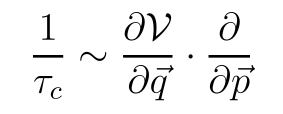

```mathematica
MaTeX["\\frac{1}{\\tau_{c}} \\sim \\frac{\\partial \\mathcal{V}}{\\partial \\vec{q}} \\cdot \\frac{\\partial}{\\partial \\vec{p}}", Magnification -> 4]
```

```mathematica
(45) -- is the typical time over which two particles are within the effective range $d$, of their interaction. For short range interactions (including van der Waals and Lenard-Jones, despite their power law decaying tails), $d \approx 10^{-10} \mathrm{~m}$ is of the order of a typical atomic size, resulting in $\tau_{c} \approx 10^{-12} s$. This is usually the shortest time scale in the problem.(45) -- In our study of particle interactions, we need to consider how long particles stay close enough to affect each other. We call this the collision time, τc. For most particles, like those with van der Waals or Lenard-Jones forces, they interact when they're about 10^-10 meters apart - about the size of an atom. This means the collision time is typically around 10^-12 seconds. This is usually the quickest event happening in our system, faster than other changes we might observe.
```

(46) -- The analysis is somewhat more complicated for long range interactions, such as the Coulomb gas in a plasma. For a neutral plasma, the Debye screening length $\lambda$ replaces $d$ in the above equation, as discussed in the problems.(46) -- When we deal with systems that have long-range interactions, like a plasma with electrically charged particles, things get a bit trickier. In a plasma where the overall charge is neutral, we use something called the Debye screening length, represented by λ, instead of the usual particle separation distance d. This Debye length helps us understand how the charges in the plasma shield each other's effects over longer distances. It's an important concept that affects how we calculate various properties of the plasma, as you'll see in the problem set at the end of this chapter.

```mathematica
(47) -- (c) There are also collision terms on the right hand side of eqs.(III.28), which depend on $f_{s+1}$, and lead to an inverse time scale(47) -- In our study of particle interactions, we encounter collision terms in our equations. These terms are related to the distribution function f_s+1 and introduce an inverse time scale. This means that as particles collide, they affect how quickly the system changes. Think of it like this: more collisions lead to faster changes in the overall behavior of the particles. These collision terms are crucial for understanding how energy and momentum are exchanged between particles in a system.
```

Statistical Mechanics
Ramirez (48)

```mathematica
MaTeX["\\frac{1}{\\tau_{\\times}} \\sim \\int d V \\frac{\\partial \\mathcal{V}}{\\partial \\vec{q}} \\cdot \\frac{\\partial}{\\partial \\vec{p}} \\frac{f_{s+1}}{f_{s}} \\sim \\int d V \\frac{\\partial \\mathcal{V}}{\\partial \\vec{q}} \\cdot \\frac{\\partial}{\\partial \\vec{p}} N \\frac{\\rho_{s+1}}{\\rho_{s}}", Magnification -> 4]
```

-Graphics-

(49) -- The integrals are only non-zero over the volume of the inter-particle potential $d^{3}$. The term $f_{s+1} / f_{s}$ is related to the probability of finding another particle per unit volume, which is roughly the particle density $n=N / V \approx 10^{26} m^{-3}$. We thus obtain the mean free time(49) -- Let's break this down into simpler terms:

When we look at particle interactions, we only need to consider the space where particles can actually affect each other. This space is determined by the inter-particle potential.

Now, imagine you're looking for another particle in a given volume. The chance of finding one is related to how many particles are typically in that space. We call this the particle density, which is just the number of particles divided by the total volume. In most cases, this is about 10.b2⁶ particles per cubic meter.

By considering these factors, we can figure out how long a particle typically travels before it bumps into another one. This is what we call the mean free time.

Statistical Mechanics
Ramirez (50)

```mathematica
MaTeX["\\tau_{\\times} \\approx \\frac{\\tau_{c}}{n d^{3}} \\approx \\frac{1}{n v d^{2}}", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["\\tau_{\\times} \\approx \\frac{\\tau_{c}}{n d^{3}} \\approx \\frac{1}{n v d^{2}}",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

τ_x≈τ_c/(n d^3)≈1/(n v d^2)

(51) -- which is the typical distance a particle travels between collisions. For short range interactions, $\tau_{\times} \approx 10^{-8} s$ is much longer than $\tau_{c}$, and the collision terms on the right hand side of eqs.(III.28) are smaller by a factor of $n d^{3} \approx\left(10^{26} \mathrm{~m}^{-3}\right)\left(10^{-10} \mathrm{~m}\right)^{3} \approx 10^{-4}$. The Boltzmann equation is obtained for short range interactions in the dilute regime by exploiting $\tau_{c} / \tau_{\times} \approx n d^{3} \ll 1$. (By contrast, for long range interactions such that $n d^{3} \gg 1$, the Vlasov equation is obtained by dropping the collision terms on the left hand side, as discussed in the problems.) From the above discussion, it is apparent that eq.(III.29) is different from the rest of the hierarchy: It is the only one in which the collision terms are absent from the left hand side. For all other equations, the right hand side is smaller by a factor of $n d^{3}$, while in eq.(III.29) it may indeed dominate the left hand side. Thus a possible approximation scheme is to truncate the equations after the first two, by setting the right hand side of eq.(III.30) to zero.(51) -- Let's break down this concept for an undergraduate student:

In a gas, particles are constantly moving and colliding with each other. The average distance a particle travels between collisions is called the mean free path. For gases with short-range interactions, the time between collisions (τ×) is about 10^-8 seconds, which is much longer than the duration of a collision (τc).

In dilute gases, where particles are far apart, we can use the Boltzmann equation to describe their behavior. This equation works well when the ratio of collision duration to time between collisions (τc/τ×) is much smaller than 1. This ratio is approximately equal to nd.b3, where n is the number of particles per cubic meter and d is the particle diameter.

For dense gases or long-range interactions, we use different equations, like the Vlasov equation, which ignores collision terms.

The key difference in the equations describing particle interactions is that the first equation (III.29) doesn't have collision terms on the left side, while all others do. This unique property of equation III.29 allows us to simplify our calculations by considering only the first two equations in the hierarchy and ignoring the rest.

```mathematica
(52) -- Setting the right hand side of the equation for $f_{2}$ to zero implies that the two body density evolves as in an isolated two-particle system. The relatively simple mechanical processes that govern this evolution result in streaming terms for $f_{2}$ which are proportional to both $\tau_{U}^{-1}$ and $\tau_{c}^{-1}$. The two sets of terms can be more or less treated independently: the former describe the evolution of the center of mass of the two particles, while the latter govern the dependence on relative coordinates.(52) -- Let's break this down into simpler terms:

When we set f₂ equal to zero, we're looking at how two particles interact when they're isolated from everything else. This interaction is governed by basic mechanical principles. These principles lead to two main effects on f₂:

1. One effect is related to τᵤ⁻.b9, which describes how the center of mass of the two particles moves.
2. The other effect is related to τ𝒸⁻.b9, which describes how the particles move relative to each other.

We can study these two effects separately to understand how the two-particle system evolves over time. This approach helps us simplify the complex behavior of many-particle systems by focusing on the fundamental two-particle interactions.
```

(53) -- The density $f_{2}$ is proportional to the joint PDF $\rho_{2}$ for finding one particle at $\left(\vec{p}_{1}, \vec{q}_{1}\right)$, and another at $\left(\vec{p}_{2}, \vec{q}_{2}\right)$, at the same time $t$. It is reasonable to expect that at distances much larger than the range of the potential $\mathcal{V}$, the particles are independent, i.e.(53) -- Let's think about how particles behave in a system. Imagine we want to know where two particles are at the same time. We use something called a density function, f₂, to help us understand this.

This density function is related to the probability of finding one particle at a certain position and momentum (p₁, q₁), and another particle at a different position and momentum (p₂, q₂).

Now, when these particles are very far apart - much farther than the range of the forces between them - we expect them to act independently. This means that knowing where one particle is doesn't tell us anything about where the other particle might be.

Statistical Mechanics
Ramirez (54)

```mathematica
MaTeX["\\begin{cases}\\rho_{2}\\left(\\vec{p}_{1}, \\vec{q}_{1}, \\vec{p}_{2}, \\vec{q}_{2}, t\\right) \\longrightarrow \\rho_{1}\\left(\\vec{p}_{1}, \\vec{q}_{1}, t\\right) \\rho_{1}\\left(\\vec{p}_{2}, \\vec{q}_{2}, t\\right), & \\text {or} \\\\ f_{2}\\left(\\vec{p}_{1}, \\vec{q}_{1}, \\vec{p}_{2}, \\vec{q}_{2}, t\\right) \\longrightarrow f_{1}\\left(\\vec{p}_{1}, \\vec{q}_{1}, t\\right) f_{1}\\left(\\vec{p}_{2}, \\vec{q}_{2}, t\\right), & \\text {for} \\quad\\left|\\vec{q}_{2}-\\vec{q}_{1}\\right| \\gg d\\end{cases}", Magnification -> 4]
```

-Graphics-

(55) -- The above statement should be true even for situations out of equilibrium. For example, imagine that the gas particles in a chamber are suddenly allowed to invade an empty volume after the removal of a barrier. The density $f_{1}$ will undergo a complicated evolution, and its relaxation time will be at least comparable to $\tau_{U}$. The two particle density $f_{2}$, will also reach its final value at a comparable time interval. However, it is expected to relax to a form similar to eq.(III.32) over a much shorter time of the order of $\tau_{c}$.(55) -- Let's think about this in a simpler way. Even when things aren't settled down (we call this "out of equilibrium"), our idea still works. Here's a fun example:

Imagine you have a box full of gas particles, and suddenly you open it up to an empty space. The gas will rush out! The way the particles spread out (we call this "density") will change in a complex way. It'll take some time for everything to settle down again.

Now, if we look at how pairs of particles behave together, that also takes about the same amount of time to settle. But here's the cool part: the way these pairs interact with each other gets back to normal much faster than the overall spreading out of the gas.

So, even though everything's chaotic for a while, some patterns come back quicker than others!

(56) -- For the collision term on the right hand side of eq.(III.29), we actually need the precise dependence of $f_{2}$ on the relative coordinates and momenta at separations comparable to $d$. At time intervals longer than $\tau_{c}$ (but possibly shorter than $\tau_{U}$ ), the 'steady state' behavior of $f_{2}$ at small relative distances is obtained by equating the largest streaming terms in eq.(III.30), i.e.(56) -- Let's think about how particles interact when they collide. To understand this, we need to look at how two particles behave when they're close to each other. We're particularly interested in their positions and how fast they're moving relative to one another.

Now, imagine we're watching these particles for a while - longer than the time it takes for a single collision, but maybe not as long as it takes for the whole system to settle down. During this time, we can see a pattern emerge in how the particles behave when they're near each other.

To describe this pattern mathematically, we focus on the most important parts of the equation that tells us how the particles move. By doing this, we can get a good idea of what's happening without getting lost in all the details.

This approach helps us understand the 'steady state' of the system - that is, how things look once the initial chaos of collisions has settled down a bit, but before everything comes to a complete equilibrium.

Statistical Mechanics
Ramirez (57)

```mathematica
MaTeX["\\left[\\frac{\\vec{p}_{1}}{m} \\cdot \\frac{\\partial}{\\partial \\vec{q}_{1}}+\\frac{\\vec{p}_{2}}{m} \\cdot \\frac{\\partial}{\\partial \\vec{q}_{2}}-\\frac{\\partial \\mathcal{V}\\left(\\vec{q}_{1}-\\vec{q}_{2}\\right)}{\\partial \\vec{q}_{1}} \\cdot\\left(\\frac{\\partial}{\\partial \\vec{p}_{1}}-\\frac{\\partial}{\\partial \\vec{p}_{2}}\\right)\\right] f_{2}=0", Magnification -> 4]
```

-Graphics-

```mathematica
(58) -- We expect $f_{2}\left(\vec{q}_{1}, \vec{q}_{2}\right)$ to have slow variations over the center of mass coordinate $\vec{Q}=\left(\vec{q}_{1}+\right.$ $\left.\vec{q}_{2}\right) / 2$, and large variations over the relative coordinate $\vec{q}=\vec{q}_{2}-\vec{q}_{1}$. Therefore, $\partial f_{2} / \partial \vec{q} \gg$ $\partial f_{2} / \partial \vec{Q}$, and $\partial f_{2} / \vec{q}_{2} \approx-\partial f_{2} / \partial \vec{q}_{1} \approx \partial f_{2} / \partial \vec{q}$, leading to(58) -- Let's think about how two particles interact with each other. We can describe their positions using two main coordinates: the center of mass (where they are on average) and their relative position (how far apart they are).

The way these particles behave doesn't change much if we move their center of mass a little. However, it changes a lot when we change how far apart they are. This means that the function describing their behavior, f₂, changes slowly with the center of mass coordinate Q, but rapidly with the relative coordinate q.

As a result, the rate of change of f₂ with respect to q is much larger than its rate of change with respect to Q. We can also say that the rate of change with respect to one particle's position is about the same as the negative of the rate of change with respect to the other particle's position.

This insight helps us simplify our calculations when studying how these particles interact.
```

Statistical Mechanics
Ramirez (59)

```mathematica
MaTeX["\\frac{\\partial \\mathcal{V}\\left(\\vec{q}_{1}-\\vec{q}_{2}\\right)}{\\partial \\vec{q}_{1}} \\cdot\\left(\\frac{\\partial}{\\partial \\vec{p}_{1}}-\\frac{\\partial}{\\partial \\vec{p}_{2}}\\right) f_{2}=-\\left(\\frac{\\vec{p}_{1}-\\vec{p}_{2}}{m}\\right) \\cdot \\frac{\\partial}{\\partial \\vec{q}} f_{2}", Magnification -> 4]
```

-Graphics-

(60) -- The above equation provides a precise mathematical expression for how $f_{2}$ is constrained along the trajectories that describe the collision of the two particles.(60) -- In simpler terms, this equation shows us exactly how the two-particle distribution function f₂ changes during a collision between two particles. It gives us a mathematical rule that f₂ must follow along the paths of these colliding particles. This helps us understand how particle interactions affect the overall behavior of a gas or fluid system.

(61) -- The collision term on the right hand side of eq.(III.29) can now be written as(61) -- Let's break down the collision term in our equation (III.29) into simpler parts. When particles bump into each other, they exchange energy and momentum. This collision process is what we're describing on the right side of our equation. We can think of it as a mathematical way to show how particles interact and change their properties during these collisions. By writing it out, we're trying to capture the essence of how these tiny particle interactions contribute to the overall behavior of the system we're studying.

Statistical Mechanics
Ramirez (62)

```mathematica
MaTeX["\\begin{aligned}\\left.\\frac{d f_{1}}{d t}\\right|_{\\text {coll.}} & =\\int d^{3} \\vec{p}_{2} d^{3} \\vec{q}_{2} \\frac{\\partial \\mathcal{V}\\left(\\vec{q}_{1}-\\vec{q}_{2}\\right)}{\\partial \\vec{q}_{1}} \\cdot\\left(\\frac{\\partial}{\\partial \\vec{p}_{1}}-\\frac{\\partial}{\\partial \\vec{p}_{2}}\\right) f_{2} \\\\& \\approx \\int d^{3} \\vec{p}_{2} d^{3} \\vec{q}\\left(\\frac{\\vec{p}_{2}-\\vec{p}_{1}}{m}\\right) \\cdot \\frac{\\partial}{\\partial \\vec{q}} f_{2}\\left(\\vec{p}_{1}, \\vec{q}_{1}, \\vec{p}_{2}, \\vec{q} ; t\\right)\\end{aligned}", Magnification -> 4]
```

-Graphics-

(63) -- The first identity if obtained from eq.(III.29) by noting that the added term proportional to $\partial f_{2} / \partial \vec{p}_{2}$ is a complete derivative and integrates to zero, while the second equality follows from eq.(III.34), after the change of variables to $\vec{q}=\vec{q}_{2}-\vec{q}_{1}$. (Since it relies on establishing the 'steady state' in the relative coordinates, this approximation is valid as long as we examine events in time with a resolution longer than $\tau_{c}$.)(63) -- Let's break this down into simpler terms:

We're looking at two important equations here. The first one comes from equation (III.29), but with a twist. We added a term that includes ∂f₂/∂p₂. Don't worry too much about what that means - the key point is that when we integrate it, it becomes zero, so it doesn't change our result.

The second equation is derived from equation (III.34). Here's where it gets a bit tricky: we changed our variables. Instead of looking at q₁ and q₂ separately, we're now looking at the difference between them (q = q₂ - q₁).

Now, this approach works well when we're dealing with what we call a 'steady state' in relative coordinates. But remember, it's only accurate if we're looking at events that happen over a time longer than τc (tau c).

```mathematica
(64) -- \begin{itemize}
  \item Kinematics of collision and scattering: The integrand in eq.(III.35) is a derivative of $f_{2}$ with respect to $\vec{q}$ along the direction of relative motion $\vec{p}=\vec{p}_{2}-\vec{p}_{1}$, of the colliding particles. To perform this integration we introduce a convenient coordinate system for $\vec{q}$, guided by the formalism used to describe the scattering of particles. Naturally, we choose one axis to be parallel to $\vec{p}_{2}-\vec{p}_{1}$, with the corresponding coordinate $a$ which is negative before a collision, and positive afterwards. The other two coordinates of $\vec{q}$ are represented by an impact vector $\vec{b}$ which is $\overrightarrow{0}$ for a head-on collision $\left(\left[\vec{p}_{1}-\vec{p}_{2}\right] \|\left[\vec{q}_{1}-\vec{q}_{2}\right]\right)$. We can now integrate over $a$ to get
\end{itemize}(64) -- Let's talk about what happens when particles collide and scatter. Imagine you're watching two particles approach each other. We can describe their motion using a special coordinate system. 

Picture a line connecting the two particles as they move towards each other. We'll call the distance along this line 'a'. Before the collision, 'a' is negative, and after the collision, it becomes positive.

Now, not all collisions are head-on. Sometimes particles graze past each other. We describe this using something called the impact vector 'b'. If 'b' is zero, it's a direct hit.

When we do calculations involving these collisions, we often need to integrate over 'a'. This helps us understand how the particles behave before and after they collide.

This approach gives us a clear picture of particle collisions and makes our calculations easier to handle.
```

Statistical Mechanics
Ramirez (65)

```mathematica
MaTeX["\\left.\\frac{d f_{1}}{d t}\\right|_{\\text {coll.}}=\\int vec{p}_{2} d \\vec{b}\\left|\\vec{v}_{1}-\\vec{v}_{2}\\right|\\left[f_{2}\\left(\\vec{p}_{1}, \\vec{q}_{1}, \\vec{p}_{2}, \\vec{b},+; t\\right)-f_{2}\\left(\\vec{p}_{1}, \\vec{q}_{1}, \\vec{p}_{2}, \\vec{b},-; t\\right)\\right]\\,  d \\", Magnification -> 4]
```

MaTeX::warn: Warning: Input ends in \. Did you forget to use \\ to denote a single backslash?

MaTeX::texerr: Error while running LaTeX.
! File ended while scanning use of \MaTeX.
!  ==> Fatal error occurred, no output PDF file produced!

$Failed

```mathematica
ToExpression[StringReplace["\\left.\\frac{d f_{1}}{d t}\\right|_{\\text {coll.}}=\\int vec{p}_{2} d \\vec{b}\\left|\\vec{v}_{1}-\\vec{v}_{2}\\right|\\left[f_{2}\\left(\\vec{p}_{1}, \\vec{q}_{1}, \\vec{p}_{2}, \\vec{b},+; t\\right)-f_{2}\\left(\\vec{p}_{1}, \\vec{q}_{1}, \\vec{p}_{2}, \\vec{b},-; t\\right)\\right]\\,  d \\",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

$Failed

(66) -- where $\left|\vec{v}_{1}-\vec{v}_{2}\right|=\left|\vec{p}_{1}-\vec{p}_{2}\right| / m$ is the relative speed of the two particles, with $(\vec{b},-)$ and $(\vec{b},+)$ referring to relative coordinates before and after the collision. Note that $d^{2} \vec{b}\left|\vec{v}_{1}-\vec{v}_{2}\right|$ is just the flux of particles impinging on the element of area $d^{2} \vec{b}$.(66) -- Let's break this down into simpler terms:

When two particles collide, we're interested in how fast they're moving relative to each other. We call this their relative speed, which we can calculate by looking at the difference in their velocities or momenta.

Before and after the collision, we use special coordinates to describe the particles' positions. We label these as (b,-) for before the collision and (b,+) for after.

Now, imagine a small area that these particles might hit. We call this area d.b2b. The number of particles hitting this area depends on both the size of the area and how fast the particles are moving relative to each other. We express this as d.b2b|v₁ - v₂|, which represents the flow of particles hitting our small area.

Understanding these concepts helps us analyze particle collisions and their effects in thermodynamic systems.

(67) -- In principle, the integration over $a$ is from $-\infty$ to $+\infty$, but as the variations of $f_{2}$ are only significant over the interaction range $d$, we can evaluate the above quantities at separations of a few $d$ from the collision point. This is a good compromise, allowing us to evaluate $f_{2}$ away from the collisions, but at small enough separations so that we can ignore the difference between $\vec{q}_{1}$ and $\vec{q}_{2}$. This amounts to a coarse-graining in space which eliminates variations on scales finer than $d$. With these provisos, it is tempting to close the equation for $f_{1}$, by using the assumption of uncorrelated particles in eq.(III.32). Clearly some care is necessary as a naive substitution gives zero! The key observation is that the densities $f_{2}$ for situations corresponding to before and after the collision have to be treated differently. For example, soon after opening of the slot separating empty and full gas containers, the momenta of the gas particles are likely to point away from the slot. Collisions will tend to randomize momenta, yielding a more isotropic distribution. However, the densities $f_{2}$ before and after the collision are related by streaming, implying that $f_{2}\left(\vec{p}_{1}, \vec{q}_{1}, \vec{p}_{2}, \vec{b},+; t\right)=f_{2}\left(\vec{p}_{1}{ }^{\prime}, \vec{q}_{1}, \vec{p}_{2}{ }^{\prime}, \vec{b},-; t\right)$, where $\vec{p}_{1}{ }^{\prime}$ and $\vec{p}_{2}{ }^{\prime}$ are momenta whose collision at an impact vector $\vec{b}$ results in production of outgoing particles with momenta $\vec{p}_{1}$\\
and $\vec{p}_{2}$. They can be obtained using time reversal symmetry, by integrating the equations of motion for incoming colliding particles of momenta $-\vec{p}_{1}$ and $-\vec{p}_{2}$. In terms of these momenta, we can write(67) -- Alright, let's simplify this concept for an undergraduate student:

When we're looking at particle collisions, we don't need to consider the entire range from negative infinity to positive infinity. Instead, we can focus on a smaller area, just a few times the size of the particle interaction range. This approach allows us to examine the particle distribution function away from the exact collision point, but still close enough that we can treat the positions of the colliding particles as essentially the same.

This method is like looking at a blurry picture of the particles - we can't see the tiniest details, but we get a good overall view of what's happening.

Now, we might be tempted to use the idea that particles are uncorrelated to simplify our equations. But we need to be careful! If we just plug in this assumption without thinking, we'll get a result of zero, which isn't helpful.

The key is to recognize that particles behave differently before and after a collision. Imagine opening a door between two rooms - one full of gas and one empty. Right after opening the door, most particles will be moving from the full room to the empty one. As time passes and collisions occur, the particle movements will become more random.

However, there's a important relationship between the particle distributions before and after a collision. If we reverse time and flip the direction of the particles' momenta, we can relate the pre-collision and post-collision states. This relationship helps us understand how collisions change the overall behavior of the gas.

Statistical Mechanics
Ramirez (68)

```mathematica
MaTeX["\\left.\\frac{d f_{1}}{d t}\\right|_{\\text {coll.}}=\\int vec{p}_{2} d \\vec{b}\\left|\\vec{v}_{1}-\\vec{v}_{2}\\right|\\left[f_{2}\\left(\\vec{p}_{1}^{\\prime}, \\vec{q}_{1}, \\vec{p}_{2}^{\\prime}, \\vec{b},-; t\\right)-f_{2}\\left(\\vec{p}_{1}, \\vec{q}_{1}, \\vec{p}_{2}, \\vec{b},-; t\\right)\\right]\\,  d \\", Magnification -> 4]
```

MaTeX::warn: Warning: Input ends in \. Did you forget to use \\ to denote a single backslash?

MaTeX::texerr: Error while running LaTeX.
! File ended while scanning use of \MaTeX.
!  ==> Fatal error occurred, no output PDF file produced!

$Failed

```mathematica
ToExpression[StringReplace["\\left.\\frac{d f_{1}}{d t}\\right|_{\\text {coll.}}=\\int vec{p}_{2} d \\vec{b}\\left|\\vec{v}_{1}-\\vec{v}_{2}\\right|\\left[f_{2}\\left(\\vec{p}_{1}^{\\prime}, \\vec{q}_{1}, \\vec{p}_{2}^{\\prime}, \\vec{b},-; t\\right)-f_{2}\\left(\\vec{p}_{1}, \\vec{q}_{1}, \\vec{p}_{2}, \\vec{b},-; t\\right)\\right]\\,  d \\",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

$Failed

```mathematica
(69) -- It is sometimes more convenient to describe the scattering of two particles in terms of the relative momenta $\vec{p}=\vec{p}_{1}-\vec{p}_{2}$ and $\vec{p}^{\prime}=\vec{p}_{1}{ }^{\prime}-\vec{p}_{2}{ }^{\prime}$, before and after the collision. For a given $\vec{b}$, the initial momentum $\vec{p}$ is deterministically transformed to the final momentum $\vec{p}^{\prime}$. To find the functional form $\vec{p}^{\prime}(|\vec{p}|, \vec{b})$, one must integrate the equations of motion. However, it is possible to make some general statements based on conservation laws: In elastic collisions, the magnitude of $\vec{p}$ is preserved, and it merely rotates to a final direction indicated by the angles $(\theta, \phi) \equiv \hat{\Omega}(\vec{b})$ (a unit vector) in spherical coordinates. Since there is a one to one correspondence between the impact vector $\vec{b}$, and the solid angle $\Omega$, we make a change of variables between the two, resulting in(69) -- Let's think about particle collisions in a simpler way. When two particles collide, we can describe their motion using their relative momenta. This means we look at how their momenta differ before and after the collision.

Before the collision, we call this difference p, and after the collision, we call it p'. The way p changes to p' depends on how the particles approach each other, which we describe using a vector b.

In elastic collisions, where no energy is lost, the size of p stays the same. It just changes direction. We can describe this new direction using two angles, θ and φ, which depend on b.

There's a direct link between b and these angles. This allows us to switch between talking about b and talking about the angles when we're doing calculations.

This approach helps us understand particle collisions without needing to solve complicated equations of motion for each particle individually.
```

Statistical Mechanics
Ramirez (70)

```mathematica
MaTeX["\\left.\\frac{d f_{1}}{d t}\\right|_{\\text {coll.}}=\\int vec{p}_{2} d \\Omega\\left|\\frac{d \\sigma}{d \\Omega}\\right|\\left|\\vec{v}_{1}-\\vec{v}_{2}\\right|\\left[f_{2}\\left(\\vec{p}_{1}^{\\prime}, \\vec{q}_{1}, \\vec{p}_{2}^{\\prime}, \\vec{b},-; t\\right)-f_{2}\\left(\\vec{p}_{1}, \\vec{q}_{1}, \\vec{p}_{2}, \\vec{b},-; t\\right)\\right]\\,  d \\", Magnification -> 4]
```

MaTeX::warn: Warning: Input ends in \. Did you forget to use \\ to denote a single backslash?

MaTeX::texerr: Error while running LaTeX.
! File ended while scanning use of \MaTeX.
!  ==> Fatal error occurred, no output PDF file produced!

$Failed

```mathematica
ToExpression[StringReplace["\\left.\\frac{d f_{1}}{d t}\\right|_{\\text {coll.}}=\\int vec{p}_{2} d \\Omega\\left|\\frac{d \\sigma}{d \\Omega}\\right|\\left|\\vec{v}_{1}-\\vec{v}_{2}\\right|\\left[f_{2}\\left(\\vec{p}_{1}^{\\prime}, \\vec{q}_{1}, \\vec{p}_{2}^{\\prime}, \\vec{b},-; t\\right)-f_{2}\\left(\\vec{p}_{1}, \\vec{q}_{1}, \\vec{p}_{2}, \\vec{b},-; t\\right)\\right]\\,  d \\",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

$Failed

(71) -- The Jacobian of this transformation, $|d \sigma / d \Omega|$, has dimensions of area, and is known as the differential cross-section. It is equal to the area presented to an incoming beam which scatters into the solid angle $\Omega$. The out-going momenta $\vec{p}_{1}{ }^{\prime}$ and $\vec{p}_{2}{ }^{\prime}$ in eq.(III.38) are now obtained from the two conditions $\vec{p}_{1}{ }^{\prime}+\vec{p}_{2}{ }^{\prime}=\vec{p}_{1}+\vec{p}_{2}$ (conservation of momentum), and $\vec{p}_{1}^{\prime}-\vec{p}_{2}^{\prime}=\left|\vec{p}_{1}-\vec{p}_{2}\right| \hat{\Omega}(\vec{b})$ (conservation of energy), as(71) -- In our study of particle collisions, we encounter a crucial concept called the differential cross-section. This quantity, represented by |dσ/dΩ|, has the dimensions of area. It tells us how much area a target particle presents to an incoming particle beam that scatters into a specific solid angle Ω.

When particles collide, their momenta change. We can find the new momenta p₁' and p₂' after the collision using two important principles:

1. Conservation of momentum: p₁' + p₂' = p₁ + p₂
2. Conservation of energy: p₁' - p₂' = |p₁ - p₂| Ω̂(b)

These equations help us understand how particles behave during and after collisions, which is fundamental to many processes in thermodynamics and statistical mechanics.

Statistical Mechanics
Ramirez (72)

```mathematica
MaTeX["\\left\\{\\begin{array}{l}\\vec{p}_{1}^{\\prime}=\\left(\\vec{p}_{1}+\\vec{p}_{2}+\\left|\\vec{p}_{1}-\\vec{p}_{2}\\right| \\hat{\\Omega}(\\vec{b})\\right) / 2 \\\\\\vec{p}_{2}^{\\prime}=\\left(\\vec{p}_{1}+\\vec{p}_{2}-\\left|\\vec{p}_{1}-\\vec{p}_{2}\\right| \\hat{\\Omega}(\\vec{b})\\right) / 2\\end{array}\\right.", Magnification -> 4]
```

-Graphics-

(73) -- For the scattering of two hard spheres of diameter $D$, it is easy to show that the scattering angle is related to the impact parameter $b$ by $\cos (\theta / 2)=b / D$ for all $\phi$. The differential cross-section is then obtained from(73) -- Let's break down the scattering of two hard spheres in a simple way. Imagine two billiard balls colliding. The diameter of each ball is D. When they hit each other, they bounce off at an angle. This angle, which we call θ (theta), depends on where exactly the balls hit each other. We measure this hitting point using something called the impact parameter, b.

Now, here's the cool part: we can relate the scattering angle to the impact parameter with a simple equation:

cos(θ/2) = b/D

This equation works no matter which direction the balls are coming from.

To figure out how likely different scattering angles are, we use something called the differential cross-section. We can calculate this using our equation above. This helps us predict how the balls will scatter in different directions after they collide.

Statistical Mechanics
Ramirez (74)

```mathematica
MaTeX["d^{2} \\sigma=b d b d \\phi=D \\cos \\left(\\frac{\\theta}{2}\\right) D \\sin \\left(\\frac{\\theta}{2}\\right) \\frac{d \\theta}{2} d \\phi=\\frac{D^{2}}{4} \\sin \\theta d \\theta d \\phi=\\frac{D^{2}}{4} d^{2} \\Omega", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["d^{2} \\sigma=b d b d \\phi=D \\cos \\left(\\frac{\\theta}{2}\\right) D \\sin \\left(\\frac{\\theta}{2}\\right) \\frac{d \\theta}{2} d \\phi=\\frac{D^{2}}{4} \\sin \\theta d \\theta d \\phi=\\frac{D^{2}}{4} d^{2} \\Omega",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

d^2 σ==b d b d ϕ==1/2 D Cos[θ/2] D Sin[θ/2] (d θ) d ϕ==1/4 D^2 sin θ d θ d ϕ==1/4 D^2 d^2 Ω

(75) -- (Note that the solid angle in three dimensions is given by $d^{2} \Omega=\sin \theta d \theta d \phi$.) Integrating over all angles leads to the total cross-section of $\sigma=\pi D^{2}$, which is evidently correct. The\\
differential cross-section for hard spheres is independent of both $\theta$ and $|\vec{P}|$. This is not the case for soft potentials. For example, the Coulomb potential $\mathcal{V}=e^{2} /|\vec{Q}|$ leads to(75) -- Let's break this down into simpler terms:

When we're dealing with hard spheres, imagine them as tiny, solid balls. The chance of these balls colliding doesn't depend on the angle they approach each other or how fast they're moving. This makes our calculations easier.

Now, if we add up all the possible ways these balls can hit each other, we get something called the total cross-section. It turns out to be π times the diameter of the ball squared. This makes sense if you think about it - it's like the area of a circle with the same diameter as our ball.

But not all particles behave like hard spheres. Some have what we call "soft potentials." These are forces that act differently depending on how close the particles are. A good example is the Coulomb potential, which describes how charged particles interact. In this case, the chance of collision does depend on the angle and speed of the particles.

Statistical Mechanics
Ramirez (76)

```mathematica
MaTeX["\\left|\\frac{d \\sigma}{d \\Omega}\\right|=\\left(\\frac{m e^{2}}{2|\\vec{P}|^{2} \\sin ^{2}(\\theta / 2)}\\right)^{2}", Magnification -> 4]
```

-Graphics-

(77) -- (The dependence on $|\vec{P}|$ can be justified by obtaining a distance of closest approach from $|\vec{P}|^{2} / m+e^{2} / b \approx 0$.)(77) -- Let's think about how close two particles can get to each other. We can find this closest distance by considering two important factors: the particles' momentum and their electrical repulsion. 

When the particles are very close, their kinetic energy (related to P.b2/m) is about equal to their electrical potential energy (e.b2/b). This balance gives us a good estimate of how near they can approach each other.

```mathematica
(78) -- \begin{itemize}
  \item The Boltzmann equation is obtained from eq.(III.38) after the substitution
\end{itemize}(78) -- Hey there! Let's talk about the Boltzmann equation. It's pretty cool, and we can get it from another equation we've seen before. Remember equation (III.38)? Well, if we make a special substitution in that equation, we end up with the Boltzmann equation. This is a super important equation in thermodynamics and statistical mechanics, as it helps us understand how gases behave on a microscopic level. It's like a bridge between the tiny world of particles and the big world we can see and measure!
```

Statistical Mechanics
Ramirez (79)

```mathematica
MaTeX["f_{2}\\left(\\vec{p}_{1}, \\vec{q}_{1}, \\vec{p}_{2}, \\vec{b},-; t\\right)=f_{1}\\left(\\vec{p}_{1}, \\vec{q}_{1}, t\\right) \\cdot f_{1}\\left(\\vec{p}_{2}, \\vec{q}_{1}, t\\right)", Magnification -> 4]
```

-Graphics-

```mathematica
(80) -- known as the assumption of molecular chaos. Note that even if one starts with an uncorrelated initial probability distribution for particles, there is no guarantee that correlations are not generated as a result of collisions. The final result is the following closed form equation for $f_{1}$(80) -- In our study of gas dynamics, we often make a key simplification called the assumption of molecular chaos. This means we treat particle collisions as if they were completely random and independent events. 

It's important to realize that even if we start with particles moving in uncorrelated ways, collisions between them could potentially create new patterns or correlations. However, for many practical purposes, we can ignore this possibility.

Using this assumption, we can derive a simplified equation for the single-particle distribution function f₁. This equation helps us describe how the particles in a gas behave overall, without needing to track every individual particle's motion.
```

Statistical Mechanics
Ramirez (81)

```mathematica
MaTeX["\\begin{aligned}& {\\left[\\frac{\\partial}{\\partial t}-\\frac{\\partial U}{\\partial \\vec{q}_{1}} \\cdot \\frac{\\partial}{\\partial \\vec{p}_{1}}+\\frac{\\vec{p}_{1}}{m} \\cdot \\frac{\\partial}{\\partial \\vec{q}_{1}}\\right] f_{1}=} \\\\& -\\int d^{3} \\vec{p}_{2} d^{2} \\Omega\\left|\\frac{d \\sigma}{d \\Omega}\\right|\\left|\\vec{v}_{1}-\\vec{v}_{2}\\right|\\left[f_{1}\\left(\\vec{p}_{1}, \\vec{q}_{1}, t\\right) f_{1}\\left(\\vec{p}_{2}, \\vec{q}_{1}, t\\right)-f_{1}\\left(\\vec{p}_{1}{}^{\\prime}, \\vec{q}_{1}, t\\right) f_{1}\\left(\\vec{p}_{2}{}^{\\prime}, \\vec{q}_{1}, t\\right)\\right]\\end{aligned}", Magnification -> 4]
```

-Graphics-

```mathematica
(82) -- Given the complexity of the above 'derivation' of the Boltzmann equation, it is appropriate to provide a heuristic explanation. The streaming terms on the left hand side of the equation describe the motion of a single particle in the external potential $U$. The collision terms on the right hand side have a simple physical interpretation: The probability of finding a particle of momentum $\vec{p}_{1}$ at $\vec{q}_{1}$ is suddenly altered if it undergoes a collision with another particle of momentum $\vec{p}_{2}$. The probability of such a collision is the product of kinematic factors described by the differential cross-section $|d \sigma / d \Omega|$, the 'flux' of incident particles proportional to $\left|\vec{v}_{2}-\vec{v}_{1}\right|$, and the joint probability of finding the two particles, approximated by $f_{1}\left(\vec{p}_{1}\right) f_{1}\left(\vec{p}_{2}\right)$. The first term on the right hand side of eq.(III.41) subtracts this probability and integrates over all possible momenta and solid angles describing the collision. The second term represents an addition to the probability which results from the inverse process: A particle can suddenly appear with coordinates $\left(\vec{p}_{1}, \vec{q}_{1}\right)$ as a result of a collision between two particles initially with momenta $\vec{p}_{1}{ }^{\prime}$ and $\vec{p}_{2}{ }^{\prime}$. The cross-section, and the momenta $\left(\vec{p}_{1}{ }^{\prime}, \vec{p}_{2}{ }^{\prime}\right)$ may have a complicated dependence on $\left(\vec{p}_{1}, \vec{p}_{2}\right)$ and $\Omega$, determined by the specific form of the potential $\mathcal{V}$. Remarkably, various equilibrium properties of the gas are quite independent of this potential.(82) -- Let's break down the Boltzmann equation in simpler terms:

The left side of the equation describes how a single particle moves in a given potential. It's like tracking a ball rolling down a hill.

The right side is all about collisions between particles. Imagine two billiard balls colliding:

1. The first term subtracts the probability of a particle being knocked out of its current state. This depends on:
   - How likely the collision is (cross-section)
   - How fast the particles are moving relative to each other
   - How many particles are around to collide with

2. The second term adds the probability of a particle ending up in this state after a collision. It's like the reverse of the first term.

These collision terms depend on the specific way particles interact. However, many important properties of gases don't actually care about these details. This is why we can often make useful predictions without knowing exactly how particles collide.
```

```mathematica
mathPiXDB1="VarsPaper23_v1.mx";
DumpSave[$WorkDir<>"mathPiXDB/"<>mathPiXDB1,"Global`"];
```

◀ prev - + prox ▶

e Guardar
d Resetear